# On Mukharnov Equation (Scalar Pert.)

## Numerical Solution

### <Aim>

Here we try to numerical solve the Muharnov equation with initial conditions being Bunch-Davis vacuum, so as to check the establishableness of the solution obained by E.D.Stewart, 1993, in the “current” case where the α_s(ϕ_N) is large.

### <Conventions>

c_s, the speed of sound is set to be 1.

τ		conformal time,
1/τ^2 f(ϕ)		z''/z(ϕ)
k		co-moving wave number, whose value is arbitrary.
τ_k		the time when k-mode crosses horizon, i.e., τ k = -1
k_N		the given scale we use,such as,for Planck,k_N =0.05 Mpc^-1
τ_N		the time when k_N-mode crosses horizon, i.e., τ_N k_N = -1
τ_I		the epoch of B-D vacuum for k_p-mode, as the initial epoch
H_I		Hubble constant at inflation epoch

### <Algorithm> %

## For Instance

For the k-mode

```mathematica
k = 0.1;
```

### Parameters

```mathematica
kN = 0.05;
τk = -1/k;
τI = 50*τk;(* set the time of epoch when the Bunch-Davis vacuum establishes. *)
τN = -1/kN;
```

```mathematica
τMin = -10000;
τMax = -1;
```

### Background part

#### Potenial

```mathematica
V[ϕ_] := ϕ^4;
ϕN = 20;
```

```mathematica
HI[τ_] := √(V[ϕ[τ]]/3);
```

#### z''/z

By the result in “expr-of-zPP-by-z.nb”, we have

```mathematica
f[ϕ_] := Evaluate[Simplify[2+10 ϵ[ϕ]^2+ϵ[ϕ] (5-9 η[ϕ])-3 η[ϕ]+η[ϕ]^2+ξ[ϕ]]];
```

where the slow-rolling parameters are, generally, defined as

```mathematica
ϵ[ϕ_] := 1/2(V'[ϕ]/V[ϕ]);
η[ϕ_] := V''[ϕ]/V[ϕ];
ξ[ϕ_] := V'[ϕ]/V[ϕ] V'''[ϕ]/V[ϕ];
```

#### ϕ(τ)

By slow-rolling assumption, we have, at ϕ_N, i.e., ϕ = 0, that is, the time when the k_p-mode crosses horizon, i.e., τ_N = -1/k_N

```mathematica
solutionOfPhi = NDSolve[{ϕ'[τ] == 1/τ V'[ϕ[τ]]/V[ϕ[τ]], ϕ[τN] == ϕN}, ϕ, {τ,τMin,τMax},AccuracyGoal->10,PrecisionGoal->20]
```

{{ϕ→InterpolatingFunction[{{-10000.,-1.}},<>]}}

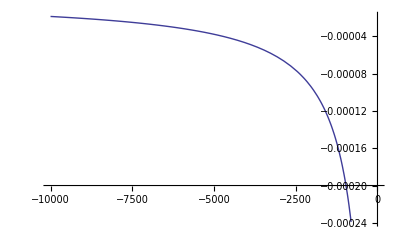

```mathematica
Plot[Evaluate[ϕ'[τ]/.solutionOfPhi], {τ, τMin, τMax}]
```

### Pert. part

#### Mukharnov equation

```mathematica
mukharnovEqu = v''[τ] + (k^2 - 1/τ^2 f[Evaluate[ϕ[τ]/.solutionOfPhi]]) v[τ];
```

```mathematica
solutionOfMukharnovEqu = NDSolve[{mukharnovEqu == 0, v[τI] == 1/(√(2k)) Exp[-I k τI],v'[τI] == -I √(k/2) Exp[-I k τI]}, v, {τ, τI, τk}]
```

{{v→InterpolatingFunction[{{-500.,-10.}},<>]}}

#### Then, the solution of ℛ

```mathematica
u[τ_] := v[τ]/z[τ];
z[τ_] := Evaluate[1/HI[τ] 1/τ V'[ϕ[τ]]/V[ϕ[τ]]/.solutionOfPhi];
```

#### Power spectrum Ps

```mathematica
ps[τ_] := k^3 Abs[u[τ]]^2
```

At horizon crossing epoch, i.e., at τ_k

```mathematica
(Evaluate[ps[τ]/.solutionOfMukharnovEqu]/.{τ -> -1/k})[[1,1]]
```

1.56193×10^6

But, the power spectrum must be a function of k.

## Shows

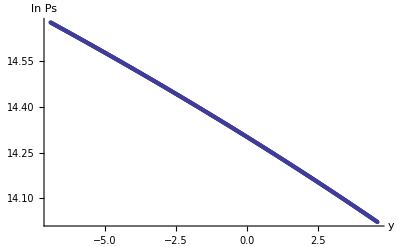
{22.8005,-Graphics-}

```mathematica
Timing[plotLnPsOfY = ListPlot[Table[{y, lnPs[y]}, {y, Log[kMin/kN], Log[kMax/kN], 0.02}], AxesLabel -> {"y", "ln Ps"}]]
```